# FernandoDuarte/LongRunRisk

Tools to solve and analyze long-run risk models

## Paclet Manifest

"Documentation"

"English"

"Guides"

"MainGuide.nb"DocumentationEnglishGuidesMainGuide.nb

"ReferencePages"

"Tutorials"

"TimeAggregation.nb"DocumentationEnglishTutorialsTimeAggregation.nb

"Kernel"

"ComputationalEngine"

"ComputeConditionalExpectations.wl"KernelComputationalEngineComputeConditionalExpectations.wl

"ComputeUnconditionalExpectations.wl"KernelComputationalEngineComputeUnconditionalExpectations.wl

"CreateMomentsDatabase.wl"KernelComputationalEngineCreateMomentsDatabase.wl

"SolveEulerEq.wl"KernelComputationalEngineSolveEulerEq.wl

"LongRunRisk.wl"KernelLongRunRisk.wl

"Model"

"Catalog.wl"KernelModelCatalog.wl

"EndogenousEq.wl"KernelModelEndogenousEq.wl

"ExogenousEq.wl"KernelModelExogenousEq.wl

"Parameters.wl"KernelModelParameters.wl

"ProcessModels.wl"KernelModelProcessModels.wl

"Shocks.wl"KernelModelShocks.wl

"Tools"

"NiceOutput.wl"KernelToolsNiceOutput.wl

"TimeAggregation.wl"KernelToolsTimeAggregation.wl

"LICENSE"LICENSE

"PacletInfo.wl"PacletInfo.wl

"README.md"README.md

"ResourceDefinition.nb"ResourceDefinition.nb

"Resources"

"BibTeX"

"references.bib"ResourcesBibTeXreferences.bib

"MaTeX-1.7.9.paclet"ResourcesMaTeX-1.7.9.paclet

"PacletizedResourceFunctions.paclet"ResourcesPacletizedResourceFunctions.paclet

"Scripts"

"PacletizeResources.wl"ScriptsPacletizeResources.wl

"Tests"

"Catalog.wlt"TestsCatalog.wlt

"ComputeConditionalExpectations.wlt"TestsComputeConditionalExpectations.wlt

"ComputeUnconditionalExpectations.wlt"TestsComputeUnconditionalExpectations.wlt

"EndogenousEq.wlt"TestsEndogenousEq.wlt

"ExogenousEq.wlt"TestsExogenousEq.wlt

"GenerateTests"

"Catalog.nb"TestsGenerateTestsCatalog.nb

"ComputeConditionalExpectations.nb"TestsGenerateTestsComputeConditionalExpectations.nb

"ComputeUnconditionalExpectations.nb"TestsGenerateTestsComputeUnconditionalExpectations.nb

"EndogenousEq.nb"TestsGenerateTestsEndogenousEq.nb

"ExogenousEq.nb"TestsGenerateTestsExogenousEq.nb

"LongRunRisk.nb"TestsGenerateTestsLongRunRisk.nb

"moments.nb"TestsGenerateTestsmoments.nb

"NiceOutput.nb"TestsGenerateTestsNiceOutput.nb

"PacletizeResources.nb"TestsGenerateTestsPacletizeResources.nb

"ProcessModels.nb"TestsGenerateTestsProcessModels.nb

"RunAllTests.nb"TestsGenerateTestsRunAllTests.nb

"Shocks.nb"TestsGenerateTestsShocks.nb

"SolveEulerEq.nb"TestsGenerateTestsSolveEulerEq.nb

"TimeAggregation.nb"TestsGenerateTestsTimeAggregation.nb

"NiceOutput.wlt"TestsNiceOutput.wlt

"PacletizeResources.wlt"TestsPacletizeResources.wlt

"ProcessModels.wlt"TestsProcessModels.wlt

"Shocks.wlt"TestsShocks.wlt

"SolveEulerEq.wlt"TestsSolveEulerEq.wlt

"TimeAggregation.wlt"TestsTimeAggregation.wlt

## Web Content

### Headline Image

### Basic Description

Tools to solve and analyze long-run risk models.

### Details

Solves long-run risk type models

Performs approximate time-aggregation

Computes moments

### Main Guide Page

### Initialization for Examples

```mathematica
PacletDirectoryLoad[NotebookDirectory[]];
```

```mathematica
(*Needs["FernandoDuarte`LongRunRisk`"];*)
Get["FernandoDuarte`LongRunRisk`"];
Needs["FernandoDuarte`LongRunRisk`Model`Parameters`"];
Needs["FernandoDuarte`LongRunRisk`Model`Shocks`"];
Needs["FernandoDuarte`LongRunRisk`Model`ExogenousEq`"];
$ContextPath=AppendTo[$ContextPath,"FernandoDuarte`LongRunRisk`Model`ExogenousEq`Private`"];
Needs["FernandoDuarte`LongRunRisk`Model`EndogenousEq`"];
$ContextPath=AppendTo[$ContextPath,"FernandoDuarte`LongRunRisk`Model`EndogenousEq`Private`"];
Get["FernandoDuarte`LongRunRisk`Model`Catalog`"];
Needs["FernandoDuarte`LongRunRisk`Model`ProcessModels`"];
Get["FernandoDuarte`LongRunRisk`ComputationalEngine`SolveEulerEq`"];
Get["FernandoDuarte`LongRunRisk`ComputationalEngine`ComputeConditionalExpectations`"];
Get["FernandoDuarte`LongRunRisk`ComputationalEngine`ComputeUnconditionalExpectations`"];
```

## Examples

### Basic Examples

Show a table with information of the available models (takes a bit of time to load the first time):

```mathematica
Models["Table"]
```

Models are defined by their parameters and state variables in an Association. Here is the Association that defines one of the models:

```mathematica
m=Models["BY"];
```

All available properties of the model:

```mathematica
Keys@m
```

{name,shortname,bibRef,desc,stateVars,parameters}

Extract properties and use them :

```mathematica
param=m["parameters"]
```

{delta→0.998,psi→1.5,gamma→10,theta→(1-gamma)/(1-1/psi),rhox→0.979,rhoxpbar→0,phix→0.044,phixc→0,mup→0,rhoppbar→0,rhop→0,phip→0,xip→0,phipc→0,phipx→0,phipcx→0,phipp→0,phipxp→0,mupbar→0,rhopbar→0,rhopbarx→0,phipbarp→0,phipbarc→0,phipbarx→0,phipbarcx→0,phipbarpb→0,phipbarxb→0,phipbarxp→0,muc→0.0015,rhocx→1,rhocp→0,phic→0,phicp→0,phicsp→0,xic→0,phics→0,phicx→1,phicc→0,phicpc→0,phicpp→0,Esg→0,rhog→0,phig→0,Esx→0.0078,vx→0.987,phisxs→2.3×10^-6,Esc→0,vc→0,phiscv→0,Esp→0,vp→0,vpp→0,vppbar→0,phispw→0,mud[1]→0.0015,rhodx[1]→3,rhodp[1]→0,phidc[1]→0,phidp[1]→0,phidsp[1]→0,xid[1]→0,phids[1]→0,phidxc[1]→0,phidcc[1]→0,phidpc[1]→0,phidpp[1]→0,phidxd[1]→4.5,phidcd[1]→0,phidpd[1]→0,taugd[1]→0}

```mathematica
delta/.param
```

0.998

```mathematica
stateVars = m["stateVars"]
```

{x[t],sx[t]}

Find coefficients of the wealth-consumption ratio, price-dividend ratio of stocks, and bond prices:

```mathematica
ms=KeySelect[models,MatchQ[#,"BKY"|"NRC"|"BS" | "DES" | "WCratio"]&];
msp=processModels[ms];
mBKY=Map[Activate,msp["BKY"]];
mBS=Map[Activate,msp["BS"]];
```

```mathematica
coeffBKY=coeff[mBKY]
coeffBS=coeff[mBS]
```

{A[0]→6.66122,A[1]→12.7003,A[2]→-2036.45,B[1][0]→5.63529,B[1][1]→64.3998,B[1][2]→-5170.5,R[0][0]→0,R[0][1]→0,R[0][2]→0,R[1][0]→-0.00106325,R[1][1]→-0.666667,R[1][2]→11.2525,R[2][0]→-0.00210373,R[2][1]→-1.31667,R[2][2]→22.8359,R[3][0]→-0.00312172,R[3][1]→-1.95042,R[3][2]→34.7421,R[4][0]→-0.00411745,R[4][1]→-2.56832,R[4][2]→46.9628,R[5][0]→-0.0050912,R[5][1]→-3.17078,R[5][2]→59.4903,R[6][0]→-0.0060432,R[6][1]→-3.75818,R[6][2]→72.3167,P[0][0]→0,P[0][1]→0,P[0][2]→0,P[1][0]→-0.00106325,P[1][1]→-0.666667,P[1][2]→11.2525,P[2][0]→-0.00210373,P[2][1]→-1.31667,P[2][2]→22.8359,P[3][0]→-0.00312172,P[3][1]→-1.95042,P[3][2]→34.7421,P[4][0]→-0.00411745,P[4][1]→-2.56832,P[4][2]→46.9628,P[5][0]→-0.0050912,P[5][1]→-3.17078,P[5][2]→59.4903,P[6][0]→-0.0060432,P[6][1]→-3.75818,P[6][2]→72.3167}

{A[0]→5.14853,A[1]→2.29875,A[2]→-6.06702,A[3]→-9892.59,A[4]→-30352.1,B[1][0]→4.28327,B[1][1]→9.68797,B[1][2]→-17.6504,B[1][3]→-42432.5,B[1][4]→-110600.,R[0][0]→0,R[0][1]→0,R[0][2]→0,R[0][3]→0,R[0][4]→0,R[1][0]→-0.00647406,R[1][1]→-0.552486,R[1][2]→0,R[1][3]→118.748,R[1][4]→827.172,R[2][0]→-0.0128407,R[2][1]→-1.,R[2][2]→0.0259669,R[2][3]→294.349,R[2][4]→1636.97,R[3][0]→-0.0191038,R[3][1]→-1.36249,R[3][2]→0.0726552,R[3][3]→515.746,R[3][4]→2436.89,R[4][0]→-0.0252665,R[4][1]→-1.6561,R[4][2]→0.13582,R[4][3]→773.912,R[4][4]→3232.82,R[5][0]→-0.0313312,R[5][1]→-1.89393,R[5][2]→0.212027,R[5][3]→1061.48,R[5][4]→4029.36,R[6][0]→-0.0373,R[6][1]→-2.08657,R[6][2]→0.298497,R[6][3]→1372.46,R[6][4]→4830.09,P[0][0]→0,P[0][1]→0,P[0][2]→0,P[0][3]→0,P[0][4]→0,P[1][0]→-0.0154589,P[1][1]→-0.552486,P[1][2]→-1.,P[1][3]→118.748,P[1][4]→827.172,P[2][0]→-0.0311478,P[2][1]→-1.,P[2][2]→-1.96203,P[2][3]→294.349,P[2][4]→1363.21,P[3][0]→-0.0470775,P[3][1]→-1.36249,P[3][2]→-2.89149,P[3][3]→515.746,P[3][4]→1625.57,P[4][0]→-0.063258,P[4][1]→-1.6561,P[4][2]→-3.79275,P[4][3]→773.912,P[4][4]→1629.76,P[5][0]→-0.0796985,P[5][1]→-1.89393,P[5][2]→-4.6694,P[5][3]→1061.48,P[5][4]→1389.69,P[6][0]→-0.0964071,P[6][1]→-2.08657,P[6][2]→-5.52436,P[6][3]→1372.46,P[6][4]→917.944}

Change one or more parameters:

```mathematica
coeff[mBKY,"parameters"->{psi->5}]
```

{A[0]→5.58261,A[1]→27.9184,A[2]→-4999.22,B[1][0]→4.6557,B[1][1]→67.2863,B[1][2]→-7711.86,R[0][0]→0,R[0][1]→0,R[0][2]→0,R[1][0]→0.00283052,R[1][1]→-0.2,R[1][2]→29.0992,R[2][0]→0.00570451,R[2][1]→-0.395,R[2][2]→58.3943,R[3][0]→0.00862192,R[3][1]→-0.585125,R[3][2]→87.8794,R[4][0]→0.0115827,R[4][1]→-0.770497,R[4][2]→117.549,R[5][0]→0.0145867,R[5][1]→-0.951234,R[5][2]→147.398,R[6][0]→0.0176339,R[6][1]→-1.12745,R[6][2]→177.42,P[0][0]→0,P[0][1]→0,P[0][2]→0,P[1][0]→0.00283052,P[1][1]→-0.2,P[1][2]→29.0992,P[2][0]→0.00570451,P[2][1]→-0.395,P[2][2]→58.3943,P[3][0]→0.00862192,P[3][1]→-0.585125,P[3][2]→87.8794,P[4][0]→0.0115827,P[4][1]→-0.770497,P[4][2]→117.549,P[5][0]→0.0145867,P[5][1]→-0.951234,P[5][2]→147.398,P[6][0]→0.0176339,P[6][1]→-1.12745,P[6][2]→177.42}

Compute moments:

```mathematica
uncondE[wc[t],mBKY]/.coeffModel
```

Compute the yield curve:

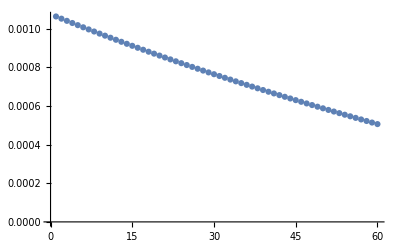

-Graphics-

```mathematica
coeffModel=coeff[mBKY,"maxMaturity"->60];
ListPlot[Table[uncondE[bondyieldeq[t,n],mBKY]/.mBKY["parameters"]/.coeffModel,{n,1,60}]]
ListPlot[Table[uncondE[nombondyieldeq[t,n],mBKY]/.mBKY["parameters"]/.coeffModel,{n,1,60}]]
```

```mathematica
Manipulate[
paramM={psi->psiM};
coeffBKY=Quiet[coeff[mBKY,"parameters"->paramM,MaxIterations->3500,"maxMaturity"->60]];
coeffBS=Quiet[coeff[mBS,"parameters"->paramM,MaxIterations->3500,"maxMaturity"->60]];
ListPlot[
Table[
{uncondE[nombondyieldeq[t,n],mBKY]/.coeffBKY//.paramM//.mBKY["parameters"],uncondE[nombondyieldeq[t,n],mBS]/.coeffBS//.paramM//.mBS["parameters"]}
,{n,1,60,12}
]ᵀ,
PlotLegends->{"BKY","BS"}
]
,{{psiM,1.1},0.5,3}]
```

```mathematica
Manipulate[
paramBKY={psi->psiBKY};
paramBS={psi->psiBS};
coeffBKY=Quiet[coeff[mBKY,"parameters"->paramBKY,MaxIterations->3500,"maxMaturity"->120]];
coeffBS=Quiet[coeff[mBS,"parameters"->paramBS,MaxIterations->3500,"maxMaturity"->120]];
ListLinePlot[
Table[
{uncondE[nombondyieldeq[t,n],mBKY]/.coeffBKY//.paramBKY//.mBKY["parameters"],uncondE[nombondyieldeq[t,n],mBS]/.coeffBS//.paramBS//.mBS["parameters"]}
,{n,1,120,12}
]ᵀ,
PlotLegends->{"BKY","BS"},FrameLabel->{"Years"},PlotLabel->"Nominal Yield Curve"
]
,{{psiBKY,psi/.mBKY["parameters"]},0.5,3},{{psiBS,psi/.mBS["parameters"]},0.5,3}]
```

```mathematica
Manipulate[
paramBS1={psi->psiBS1};
paramBS2={psi->psiBS2};
coeffBS1=Quiet[coeff[mBS,"parameters"->paramBS1,MaxIterations->3500,"maxMaturity"->120]];
coeffBS2=Quiet[coeff[mBS,"parameters"->paramBS2,MaxIterations->3500,"maxMaturity"->120]];
ListLinePlot[
Table[
{uncondE[nombondyieldeq[t,n],mBS]/.coeffBS1//.paramBS1,uncondE[nombondyieldeq[t,n],mBS]/.coeffBS2//.paramBS2}//.mBS["parameters"]
,{n,1,120,12}
]ᵀ,
PlotLegends->{"BS1","BS2"},FrameLabel->{"Years"},PlotLabel->"Nominal Yield Curve"
]
,{{psiBS1,psi/.mBS["parameters"]},0.5,5},{{psiBS2,0.5+psi/.mBS["parameters"]},0.5,5}]
```

Change one or more parameters:

```mathematica
moments[m,"gamma"->5]
```

Get more information about some of the models:

```mathematica
ms=KeySelect[models,MatchQ[#,"BKY"|"NRC" | "BY" ]&];
msP=processModels[ms];
msP["BY"]
```

processModels[KeySelect[models,MatchQ[#1,BKY|NRC|BY]&]][BY]

Create a very interesting Plot:

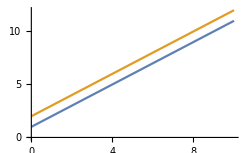

```mathematica
Plot[{AddOne[x],AddTwo[x]},{x,0,10}]
```

### Scope

Add to symbols:

```mathematica
AddOne[x]
```

1+x

```mathematica
AddTwo[x]
```

2+x

Create new functions that no one has ever thought of before:

```mathematica
addThree=AddOne@*AddTwo
```

AddOne@*AddTwo

```mathematica
addThree[1]
```

4

```mathematica
naturalNumber[n_]:=Nest[AddOne,0,n];
```

Simply incredible:

```mathematica
naturalNumber[5]
```

5

### Applications

Reinvent arithmetic:

```mathematica
plus[x_,y_]:=Nest[AddOne,x,y];
```

```mathematica
plus[3,4]
```

7

```mathematica
times[x_,y_]:=Nest[OperatorApplied[plus][x],0,y];
```

```mathematica
times[3,4]
```

12

Weird numbers like negative integers and reals are too hard and can therefore be assumed to not exist.

### Properties and Relations

AddTwo can be implemented using only AddOne:

```mathematica
AddTwo[x]
```

2+x

```mathematica
addTwo=AddOne@*AddOne;
```

```mathematica
addTwo[x]
```

2+x

AddOne is the best function:

```mathematica
[Row[{AddOne," is simply the best"}]]
```

-Graphics-

## Source & Additional Information

### Creator

Fernando Duarte

### Source Control Repository

https://github.com/GitHub-at-Brown/LongRunRisk

### License

MIT License [»](https://resources.wolframcloud.com/PacletRepository/licenses/MIT)
 Apache License 2.0 [»](https://resources.wolframcloud.com/PacletRepository/licenses/Apache-2.0)
 Creative Commons Zero v1.0 Universal [»](https://resources.wolframcloud.com/PacletRepository/licenses/CC0-1.0)
 NoneA license is not required for personal deployments

### Keywords

Economics

Finance

Asset Pricing

CI/CD

GitHub

### Categories

Cloud & Deployment
 Data Manipulation & Analysis
 External Interfaces & Connections
 Geographic Data & Computation
 Graphs & Networks
 Images
 Machine Learning
 Scientific and Medical Data & Computation
 Sound & Video
 Symbolic & Numeric Computation
 Time-Related Computation
 Visualization & Graphics |  Core Language & Structure
 Engineering Data & Computation
 Financial Data & Computation
 Geometry
 Higher Mathematical Computation
 Knowledge Representation & Natural Language
 Notebook Documents & Presentation
 Social, Cultural & Linguistic Data
 Strings & Text
 System Operation & Setup
 User Interface Construction

### Related Resource Objects

### Original Source References and Attributions

Source, reference or citation

### Links

GitHub

### Compatibility

#### Wolfram Language Version

13.0+

#### Operating System

Windows |  Mac |  Linux

#### Environments

SessionLocal or cloud interactive session
 WebEvaluationCloud evaluation initiated by an HTTP request
 BatchJobRemote batch job |  ScriptScript run in batch mode
 WebAPIAPI called through an HTTP request
 |  SubkernelParallel or grid subkernel
 ScheduledScheduled task

#### Cloud Support

Supported in cloud

#### Required Features

Notebooks |  Parallel Kernels |  Cloud Access

### Disclosures

Local filesDisclosuresLocalFilesChoose this option if your paclet directly does any of the following during loading or normal usage:
◼ Creates, deletes or modifies local files
◼ Imports data from local files
File operations related to normal paclet installation and loading are excepted.Click for more information

Wolfram accountDisclosuresWolframAccountChoose this option if your paclet directly does any of the following:
◼ Requires, uses, or records any information related to user’s Wolfram ID
◼ Interacts with the user’s Cloud account or Wolfram account
◼ Creates, deletes or modifies the user’s cloud objects
◼ Creates or executes cloud deployed scheduled tasks
◼ Uses cloud credits, service credits or Wolfram credits
◼ Makes WolframAlpha callsClick for more information

External servicesDisclosuresExternalServicesChoose this option if your paclet directly does any of the following:
◼ Makes requests to external services (http, ftp, ssh, etc)
◼ Creates or uses service connection
◼ Send emailsClick for more information

WL system configurationDisclosuresWLSystemConfigurationChoose this option if your paclet directly does any of the following:
◼ Creates persistent local scheduled tasks
◼ Modifies WL system or environment settings
◼ Modifies $Path, Directory, or similar
◼ Installs additional paclets or dependencies
◼ Creates or imports non-public ResourceObject content
◼ Makes FrontEnd modifications
◼ Internal handlersClick for more information

WL built-in symbolsDisclosuresWLSystemSymbolsChoose this option if your paclet directly modifies definitions of built-in symbols such as those in System` or other internal contexts.Click for more information

Paclet dependenciesDisclosuresPacletDependenciesChoose this option if your paclet directly installs or updates any additional paclets. Paclets that are included with the Wolfram system do not require a disclosure.Click for more information

OS configurationDisclosuresOSConfigurationChoose this option if your paclet directly does any of the following:
◼ Modifies OS settings
◼ Makes any use of SystemCredentialClick for more information

Local system interactionsDisclosuresLocalSystemInteractionsChoose this option if your paclet directly does any of the following:
◼ Executes Shell or RUN commands
◼ Uses external evaluators via ExternalEvaluate
◼ Interacts with external libraries
◼ Reads or writes to streams or sockets
◼ Launches parallel kernels, subkernels or GPUsClick for more information

OtherDisclosuresOtherAdd additional text as needed in a new cell below to document any additional disclosures that are not listed above.Click for more information

## Author Notes

Additional information about limitations, issues, etc.